```mathematica
SetDirectory["/Users/keitokiddo/VC_revision/Simulations/2_16_DEN"];
```

```mathematica
noiseprops={0.05, 0.1, 0.2, 0.3, 0.4, 0.5, 0.8};
```

```mathematica
varnoise = .25 * Variance[fs[[1]]//Flatten]
```

0.25

```mathematica
(1/(1-#) -1)&/@noiseprops
```

{0.0526316,0.111111,0.25,0.428571,0.666667,1.,4.}

```mathematica
varnoiselist = (1/(1-#) -1)&/@noiseprops * Variance[fs[[1]]//Flatten]
```

{0.0526316,0.111111,0.25,0.428571,0.666667,1.,4.}

```mathematica
noisevecslist = Table[RandomVariate[NormalDistribution[0, Sqrt[varnoiselist[[i]]]], alpha^l], nrep,{i,Length@noiseprops}];
```

```mathematica
noisevecslist//Dimensions
```

{3,7,65536}

```mathematica
fnlist=Table[fs[[j]]+noisevecslist[[j,i]], {j,nrep},{i,Length@noiseprops}];
```

```mathematica
fnlist//Dimensions
```

{3,7,65536}

```mathematica
Table[r2[fnlist[[1,i]], fs[[1]]],{i,Length@noiseprops}]
```

{0.949848,0.900526,0.801001,0.701729,0.602558,0.501698,0.197417}

```mathematica
Do[Export[StringJoin["data/",fl,  "_f_","noised_", ToString[i],"_", ToString[j],".tsv"],fnlist[[i,j]],"TSV"],{i,nrep},{j,Length@noiseprops}]
```

varlist=[0.00011985,0.000253016,0.000569287,0.000975921,0.0015181,0.00227715,0.00910859]

varall = 0.000569287*np.ones(G)

f = 'f_noised'
train = 'tr'
scheme = 'noised'


for i in range(3):
    for k in range(7):
        varall = varlist[k]*np.ones(G)
        for j in range(13):
            response_name = [fl_name, f, str(i+1), str(k+1)]
            tr_name = [train, str(j + 1)]
            map_name = [fl_name, scheme, "vc", str(i + 1), str(k+1), str(j + 1)]
            lda_name = [fl_name, scheme, "lda", str(i + 1), str(k+1), str(j + 1)]
            response = pd.read_csv(dirin + "_".join(response_name) + ".tsv", header = None)
            response = response.to_numpy()
            response = response.squeeze()
            print(tr_name, map_name, response_name, lda_name)
            print("working on sample " + str(i+1) + "," str(k+1) + "," + str(j+1))
            tr = pd.read_csv(dirin + "_".join(tr_name) + ".tsv", header = None)
            tr = np.array(tr).flatten()
            tr -= 1 
            lambdas,map = vc.compute_posterior_mean_ex(
                np.array(seqs)[tr], np.array(response)[tr], np.array(varall)[tr])
            pd.DataFrame(map).to_csv(dirout + "_".join(map_name) + ".tsv", header = None, index = None)
            pd.DataFrame(lambdas).to_csv(dirout + "_".join(lda_name) + ".tsv", header = None, index = None)

```mathematica
pdsVClist=Table[{},3,7,13 ];
```

```mathematica
lgs=Table[Length[pdsVClist[[i,j,k]]],{i,3},{j,7},{k,13}]
```

{{{65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536},{65536,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0}},{{65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0}},{{65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
lgs[[i,j,k]]
```

0

```mathematica
lgs[[k,i,j]]
```

0

```mathematica
k=1;
i=2;
j=1;
```

```mathematica
i=1
j=2
k=1
```

1

2

1

```mathematica
lgs[[i,k,j]]
```

65536

```mathematica
pdsVClist[[i,j,k]]
```

{-0.00264759,-0.014898,0.0181459,0.0205357,0.00669836,-0.00757334,0.013252,0.0012356,-0.00645584,-0.0375724,0.0058031,65514,0.0328781,0.0180976,0.0278704,-0.00109362,0.0565494,-0.0130827,0.0374403,0.00353534,0.0215677,0.0155674,0.0253929}
 |  |  |  |

```mathematica
pdsVClist[[i,j,k]]=Import[StringJoin["out/",StringRiffle[{fl,  "noised","vc",ToString[k], ToString[i], ToString[j]},"_"],".tsv"]]//Flatten
```

{-0.00264759,-0.014898,0.0181459,0.0205357,0.00669836,-0.00757334,0.013252,0.0012356,-0.00645584,-0.0375724,0.0058031,65514,0.0328781,0.0180976,0.0278704,-0.00109362,0.0565494,-0.0130827,0.0374403,0.00353534,0.0215677,0.0155674,0.0253929}
 |  |  |  |

```mathematica
Do[Import[StringJoin["out/",StringRiffle[{fl,  "noised","vc",ToString[k], ToString[i], ToString[j]},"_"],".tsv"]]//Flatten,{k,nrep},{i,7},{j,Length@proportions}]
```

```mathematica
Do[pdsVClist[[k,i,j]]=Import[StringJoin["out/",StringRiffle[{fl,  "noised","vc",ToString[k], ToString[i], ToString[j]},"_"],".tsv"]]//Flatten,{k,nrep},{i,7},{j,Length@proportions}]
```

```mathematica
TableForm[Transpose@{Range[Length@proportions],proportions//N}]
```

1 | 0.00999451
2 | 0.0500031
3 | 0.100006
4 | 0.199997
5 | 0.300003
6 | 0.399994
7 | 0.5
8 | 0.600006
9 | 0.699997
10 | 0.800003
11 | 0.899994
12 | 0.949997
13 | 0.990005

```mathematica
pdsVCtrueldalist=Table[{},3,7,13 ];
```

```mathematica
Do[pdsVCtrueldalist[[i,k,j]]=Import[StringJoin["out/",fl,  "_noised_","vc_tru_lda_", ToString[i],"_",ToString[k],"_",  ToString[j],".tsv"]]//Flatten,{i,nrep},{k,7},{j,Length@proportions}]
```

#### Import FL

```mathematica
fs=Table[{},nrep];
Do[fs[[i]]=Import[StringJoin["data/",fl,  "_f_", ToString[i],".tsv"]]//Flatten,{i,nrep}];
fns=Table[{},nrep];
Do[fns[[i]]=Import[StringJoin["data/",fl,  "_f_","noised_", ToString[i],".tsv"]]//Flatten,{i,nrep}];
```

#### Import training samples

```mathematica
trs=Table[{},Length@proportions];
Do[trs[[i]]=Import[StringJoin["data/", "tr_",ToString[i],".tsv"]]//Flatten,{i,Length@proportions}]
tts=Table[Complement[Range[alpha^l],trs[[i]]],{i,Length[trs]}];
```

```mathematica
j=12;
```

```mathematica
trr2list=Table[r2[pdsVClist[[i,k,j]][[trs[[j]]]],fs[[i]][[trs[[j]]]]],{i,nrep},{k,7}]
```

{{0.00129813,0.00138269,0.00123948,0.00169964,0.00176037,0.00167838,0.00139025},{5.86767×10^-6,8.47967×10^-7,3.37495×10^-7,4.16653×10^-6,0.0000246578,2.93883×10^-6,4.05366×10^-6},{0.00027874,0.000419482,0.000388517,0.0006227,0.000379922,0.000562075,0.00037476}}

```mathematica
plotdat=Table[{Around[noiseprops[[k]],0],Around[Median[trr2list[[All,k]]],StandardDeviation[trr2list[[All,k]]]]},{k,7}]
```

{{0.05,0.965050.00033},{0.1,0.938490.00033},{0.2,0.892350.00032},{0.3,0.84980.0011},{0.4,0.80760.0007},{0.5,0.75790.0013},{0.8,0.56260.0028}}

```mathematica
trr2truldalist=Table[r2[pdsVCtrueldalist[[i,k,j]][[trs[[j]]]],fs[[i]][[trs[[j]]]]],{i,nrep},{k,7}]
```

{{0.965051,0.938322,0.892352,0.851089,0.807727,0.757633,0.564639},{0.964853,0.938488,0.892346,0.848937,0.807658,0.757985,0.559561},{0.965497,0.938964,0.892904,0.849828,0.806432,0.760005,0.562573}}

```mathematica
plotdattrulda=Table[{Around[noiseprops[[k]],0],Around[Median[trr2truldalist[[All,k]]],StandardDeviation[trr2truldalist[[All,k]]]]},{k,7}]
```

{{0.05,0.965050.00033},{0.1,0.938490.00033},{0.2,0.892350.00032},{0.3,0.84980.0011},{0.4,0.80770.0007},{0.5,0.75800.0013},{0.8,0.56260.0026}}

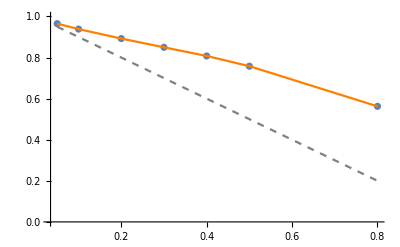

```mathematica
Show[
ListPlot[plotdat,PlotRange->{All,{0,1}}],
ListPlot[plotdattrulda,PlotRange->{All,{0,1}},PlotStyle->Orange,Joined->True],
ListLinePlot[Transpose@{noiseprops,1-noiseprops},
PlotStyle->Directive[Gray,Dashed]]
]
```

```mathematica
lambdas//N
```

{1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7}

### Plotting reconstruction and test R2 against noise and training density

```mathematica
colors=ColorData["Rainbow"][#]&/@proportions
```

{RGBColor[0.4457697734375, 0.11017546533203125, 0.5489963991699219],RGBColor[0.34312257031250004, 0.11581763037109376, 0.6369851115722656],RGBColor[0.274854908203125, 0.1822741279296875, 0.7272890229492187],RGBColor[0.24848732373046875, 0.38632027587890627, 0.8133736618652344],RGBColor[0.29796154321289064, 0.5657976296386719, 0.7522355305175782],RGBColor[0.3882180263671875, 0.6741904990234374, 0.6035538901367188],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.6660927104492188, 0.7430416899414063, 0.32292959716796876],RGBColor[0.8083382326660156, 0.7110830603027344, 0.2559771848144531],RGBColor[0.8935154311523438, 0.6004107058105468, 0.22054542236328126],RGBColor[0.8929570166015625, 0.38967729882812496, 0.17940387939453126],RGBColor[0.8739584130859375, 0.2607955151367188, 0.15481178442382815],RGBColor[0.8606768564453124, 0.15702807275390626, 0.13666198803710938]}

```mathematica
trr2list=Table[r2[pdsVClist[[i,k,j]][[trs[[j]]]],fs[[i]][[trs[[j]]]]],{j,13},{i,nrep},{k,7}];
```

```mathematica
trr2list//Dimensions
```

{13,3,7}

```mathematica
plotdat=Table[{Around[noiseprops[[k]],0],Around[Median[trr2list[[j,All,k]]],StandardDeviation[trr2list[[j,All,k]]]]},{j,13},{k,7}];
```

```mathematica
plotdat//Dimensions
```

{13,7,2}

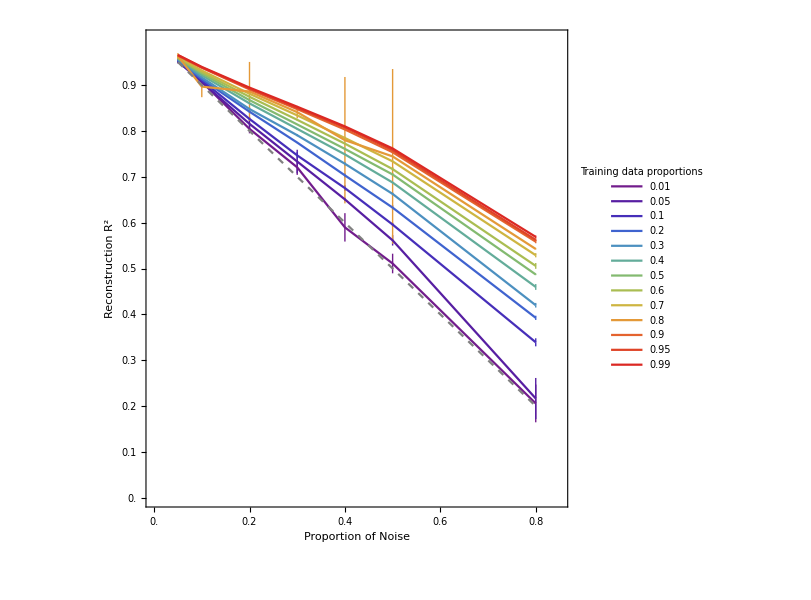

```mathematica
figtr=Show[
ListPlot[plotdat,Joined->True,
PlotLegends->Placed[leg,Top],
PlotStyle->colors,
BaseStyle->{FontSize->fontsize},
AspectRatio->1,
PlotRange->{{0,.85},{0,1}},
Frame->True,
PlotStyle->style,
FrameStyle->fstyle,
FrameTicks->{{Range[0,.9,.1],False},{Range[0,.9,.1],False}},FrameLabel->{"Proportion of Noise","Reconstruction "Superscript[R,2]}],
ListLinePlot[Transpose@{noiseprops,1-noiseprops},
PlotStyle->Directive[Gray,Dashed]], ImageSize->600
]
```

```mathematica
tsr2list=Table[r2[pdsVClist[[i,k,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{j,13},{i,nrep},{k,7}];
```

```mathematica
plotdat=Table[{Around[noiseprops[[k]],0],Around[Median[tsr2list[[j,All,k]]],StandardDeviation[tsr2list[[j,All,k]]]]},{j,13},{k,7}];
```

```mathematica
leg=PointLegend[Round[proportions//N,.01],LegendLabel->"Training data proportions",LegendFunction->"Frame",LegendLayout->"Row",LegendMarkers->Automatic];
```

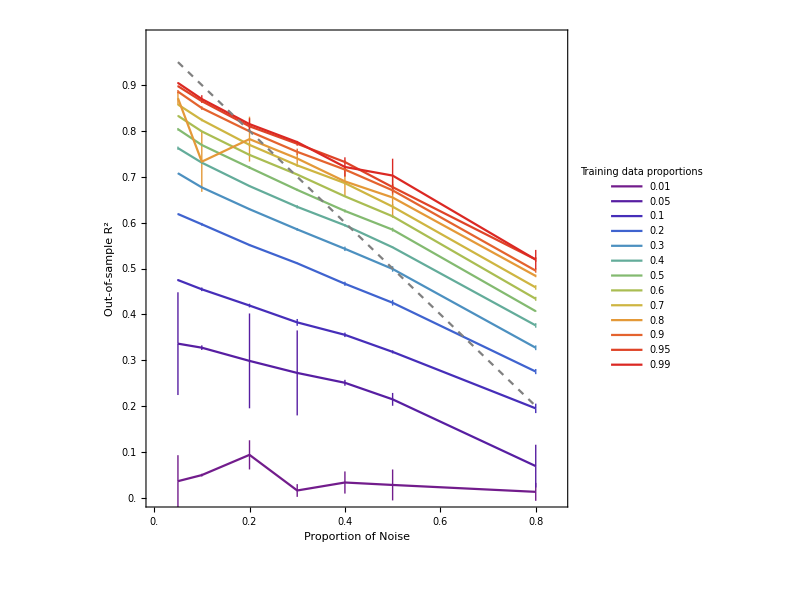

```mathematica
figts=Show[
ListPlot[plotdat,Joined->True,
PlotLegends->Placed[leg,Top],
PlotStyle->colors,
BaseStyle->{FontSize->fontsize},
AspectRatio->1,
PlotRange->{{0,.85},{0,1}},
Frame->True,
PlotStyle->style,
FrameStyle->fstyle,
FrameTicks->{{Range[0,.9,.1],False},{Range[0,.9,.1],False}},FrameLabel->{"Proportion of Noise","Out-of-sample "Superscript[R,2]}],
ListLinePlot[Transpose@{noiseprops,1-noiseprops},
PlotStyle->Directive[Gray,Dashed]], ImageSize->600
]
```

```mathematica
Grid[{{figtr,figts}},Spacings->2{1, 1}]
```

-Graphics- | -Graphics-

```mathematica
Export["../figs/2_16_DEN_Noise.pdf",%]
```

../figs/2_16_DEN_Noise.pdf